```mathematica
(*Funcion para importar los datos*)
importData[dir_]:=Module[{data,lambda,dataRF},
data=Import[dir];
lambda=data[[All,1]];
dataRF=Transpose[{lambda,data[[All,2]]}]]
```

```mathematica
Glass4000=importData["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-licenciatura\\CST\\Glass_sph_4000nm.csv"];
Glass4000bck1000=importData["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-licenciatura\\CST\\Glass_sph_4000nm_bck1000.csv"];
```

```mathematica
ListPlot[{gCscaMie,Glass4000,Glass4000bck1000},PlotLegends->Automatic]
```

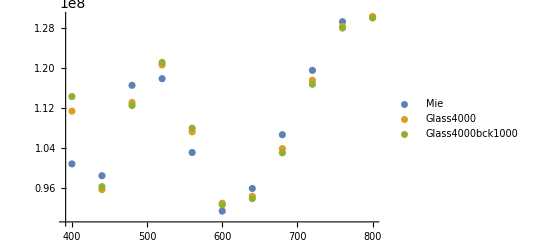

```mathematica
Glass4000[[All,2]][[1]]-gCscaMie[[All,2]][[1]]
```

1.05586×10^7